Your Title Here

```mathematica
Manipulate[
Module[{θ,τp,Gp},
θ=1;(*dead time*)
τp=2;(*process time constant*)

Gp=TransferFunctionModel[{{kc*kp*Exp[-θ*s]*(τI*s+1)*(τD*s+1)/((τp*s+1)*τI*s)}},s];

BodePlot[Gp,{0.1,100},PlotStyle->{{Thick,Black}},PlotRange->{{{0.1,100},All},{{0.1,100},All}},
Frame->True,FrameLabel->{{None,"magnitude (dB)"},{"frequency","phase (degrees)"}},LabelStyle->{{17,Black},{17,Black}},ImageSize->{{600,200},{600,200}},AspectRatio->Full,GridLines->Automatic,
Epilog->{
{Thick,Blue,Line[{{Log10@x,40},{Log10@x,-15}}]},
{Thick,Blue,Line[{{Log10@x,-5840},{Log10@x,2500}}]}
}]
],
Grid[{
{Control[{{kp,8.6,Row@{"process gain ",Subscript[Style["K",Italic],"P"]}},-10,10,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft,
Control[{{kc,1,Row@{"controller gain ",Subscript[Style["K",Italic],"C"]}},1,10,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft},
{Control[{{τI,1,Row@{"integral time constant ",Subscript[Style["τ",Italic],"I"]}},1,50,Appearance->"Labeled",ImageSize->Small}],
Control[{{τD,3,Row@{"derivative time constant ",Subscript[Style["τ",Italic],"D"]}},1,20,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft},
{Control[{{x,1},0.1,100,0.1,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```

```mathematica
(*Overlay[{
BodePlot[Gp,{0.1,100},PlotStyle->{{Thick,Black}},PlotRangePadding->{None,Scaled@0.05},Frame->True,FrameLabel->{None,"magnitude (dB)"},LabelStyle->{17,Black},ImageSize->{600,200},AspectRatio->Full,GridLines->Automatic,PlotLayout->"Magnitude",PlotRangeClipping->False,
Epilog->{Red,Line[{{Log10@x,40},{Log10@x,-10}}]}],
BodePlot[Gp,{0.1,100},PlotStyle->{{Thick,Black}},PlotRange->{-4000,4000},PlotRangePadding->{None,Scaled@0.05},Frame->True,FrameStyle->Red,FrameLabel->{"frequency","phase (degrees)"},LabelStyle->{17,Black},ImageSize->{600,200},AspectRatio->Full,GridLines->Automatic,PlotLayout->"Phase",PlotRangeClipping->False,ImagePadding->{{45,13},{30,5}}]
}]*)
```

```mathematica
N@Log@2
```

0.693147

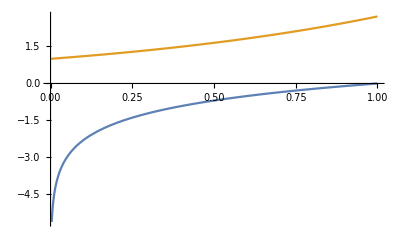

```mathematica
Plot[{Log@x,Exp@x},{x,0,1}]
```

```mathematica
(*Grid[{
{Style["gain:",Bold],
Control[{{kp,8.6,Row@{"process ",Subscript[Style["K",Italic],"P"]}},-10,10,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft,
Control[{{kc,1,Row@{"controller ",Subscript[Style["K",Italic],"C"]}},1,10,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft},
{Style["time constant:",Bold],SpanFromLeft,
Control[{{τI,1,Row@{"integral ",Subscript[Style["τ",Italic],"I"]}},1,50,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft,
Control[{{τD,3,Row@{"derivative ",Subscript[Style["τ",Italic],"D"]}},1,20,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left]*)
```





```mathematica
(*Overlay[{
BodePlot[Gp,{0.1,100},PlotStyle->{{Thick,Black}},PlotRangePadding->{{None,Scaled@0.05},{None,{None,Scaled@0.05}}},Frame->True,FrameLabel->{{None,"magnitude (dB)"},{"frequency","phase (degrees)"}},LabelStyle->{{17,Black},{17,Black}},ImageSize->{{600,200},{600,200}},AspectRatio->Full,GridLines->Automatic],
Graphics[{
(*Red,Line[{{Log@#,0},{Log@#,1}}]&/@Range[0,100],*)
Thick,Dashed,Blue,Line[{{Exp@x,0},{Exp@x,1}}]
},Frame->True,PlotRange->{{0.1,100},All},ImageSize->{600,400},AspectRatio->Full,ImagePadding->{{75,15},{35,5}}]
}]*)
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX